# Obora Roman, 2 course ,FKN ,course computer mathematic, var. 3.

## Тема 1. Введення в систему Mathematica.

## Завдання 1. Арифметичні обчислення.

Задача 1.1.3. Обчислити значення арифметичного виразу.

```mathematica
((215+9/16)-(208+3/4)+1/2)/(0.0001/0.005)
```

365.625

## Завдання 2 Обчислення виразу з елементарними функціями

Задача 1.2.3. Використовуючи систему «Mathematica», обчислити вираз.

```mathematica
y = Tan[Log[1/3]]+Sin[4 √3]^2/(4Cos[√8])
```

1/4 Sec[2 √2] Sin[4 √3]^2-Tan[Log[3]]

## Тема 2. Алгебраїчні обчислення.

Завдання 1.Алгебраїчні перетворення.

Задача 2.1.3. Використовуючи систему «Mathematica», спростити вираз

```mathematica
Remove[a,x]
Simplify[(2 a)/(a^2-4 x^2)+1/(2 x^2+6 x-a x-3 a)*(x+(3 x-6)/(x-2))]
```

1/(a+2 x)

Завдання 2. Обчислення значень алгебраїчних виразів.

Задача 2.2.3. Використовуючи систему «Mathematica», обчислити значення виразу при вказаних значеннях параметрів

```mathematica
Remove[a,x]
Simplify[(((a^2 x)^(1/6)+√x)/(x^(1/3)+a^(1/3))+x^(1/6))^3+4*(x+1)+((x √x)^(1/3)+1)^2/.{a->1, x->4}]
```

45

Завдання 3. Розв’язання рівнянь.

Задача 2.3.3. Використовуючи систему «Mathematica», розв’язати рівняння

```mathematica
Remove[a,b,x]
Simplify[Solve[(x-a-b)/c+(x-b-c)/a+(x-c-a)/b==3]]
```

{{c→-(a b)/(a+b)},{x→a+b+c}}

## Тема 3. Елементи аналітичної геометрії.

Завдання 1. Робота з векторами.

Задача 3.1.3. Використовуючи систему «Mathematica», з’ясувати, чи колінеарні вектори c1 і c2, які побудовані по векторам a та b. Знайти довжину векторів a і b, та кут між ними. В системі Mathematica намалювати вектори a і b.

```mathematica
Remove[a,b,c1,c2,z]
```

```mathematica
a={−2,4,1};b={1,−2,7};
c1= 5 a+3 b;c2=2 a -b;
z = {0,0,0};
с1/с2
Norm[a]
Norm[b]
(N[VectorAngle[a,b]]*180)/π
Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{z,a}],Arrow[{z,b}]},Axes->True,AxesLabel->{"X","Y","Z"}]
```

с1/с2

√21

3 √6

95.1111

-Graphics3D-

Завдання 2. Геометричні обчислення в трикутнику.

Задача 3.2.3. Використовуючи систему «Mathematica», знайти довжини сторін,величини кутів та площу трикутника з вершинами в точках A, B, C.

```mathematica
Unprotect[C,B]
Remove[A,B,C,S]
A={3,3,-1}
B={5,5,-2}
C={4,4,1}
ListPlot3D[{A,B,C},BoxRatios->Automatic]
AB = B-A
AC = C-A
BC=C-B
LAB=Nor[AB];
LAC=Norm[AC];
LBC=Norm[BC];
{LAB,LAC,LBC}
aA=VectorAngle[AB,AC];
aB=VectorAngle[-AB,BC];
aC=VectorAngle[AC,BC];
{aC,aB,aC}
N[{aA,aB,aC} 180/π]
S = 1/2 Norm[Cross[AB,AC]]
```

{}

{3,3,-1}

{5,5,-2}

{4,4,1}

-Graphics3D-

{2,2,-1}

{1,1,2}

{-1,-1,3}

{!{2,2,-1},√6,√11}

{ArcCos[2 √(2/33)],ArcCos[7/(3 √11)],ArcCos[2 √(2/33)]}

{74.2068,45.2894,60.5038}

5/(√2)

```mathematica
{}
```

{}

Завдання 3. Геометричні обчислення в тетраедрі.

Задача 3.3.3. Використовуючи систему «Mathematica», обчислити об’ємтетраедра з вершинами в точках A,B,C,D, та його висоту, яка випущена звершини D на грань ABC. Графічно зобразити тетраедр і його висоту.

```mathematica
Unprotect[C,D,E];
Remove[A,B,C,D,p1,AB,AC,AD,V,n,S,hh,h,E,p2,p3]
A={0,0,0};
B={2,1,0};
C={1,2,0};
D={1.3,1.1,2};
p1 = Graphics3D[{Thickness[0.02],Line[{A,B,C,A,D,B,C,D}]},AxesLabel->{"X","Y","Z"},Axes->True];
AB = B-A;
AC = C-A;
AD=D-A;
V=1/6 Abs[Det[{AB,AC,AD}]]
n=Cross[AB,AC];
S=1/2 Norm[n]
hh=Solve[1/3 S h==V,h] 
h=hh[[1,1,2]];
E=D-n/Norm[n] h;
p2=ListPointPlot3D[{E},PlotStyle->{Directive[PointSize[0.006],Red]}];
p3 = Graphics3D[{Thickness[0.002],Line[{D,E}]}];
Show[p1,p2,p3]
```

1.

3/2

{{h→2.}}

-Graphics3D-

## Тема 4. Матричне числення.

Завдання 1. Матричне числення

Задача 4.1.3 Використовуючи систему «Mathematica», знайти значення матричного многочлена2A^2+3A+5E, якщо E одинична матриця. Знайти обернену матрицю A^-1. Обчислити визначник матриці A. Обчислити суму тарізницю матриць A і B. Обчислити матричний A.Bта поелементний добуток A*B матриць, обчислити різницю між цими добутками. Розв’язати матричне рівняння AX =B відносно матриці X.

```mathematica
Remove[A,M,B,X,A1]
A={{0,2,3},{4,1,0},{2,-1,-2}}
M= 2*A.A+3*A+5*IdentityMatrix[3];
A1=Inverse[A]
MatrixForm[A1]
Det[A]
B={{1,2,0},{3,0,-1},{2,1,-1}};
A+B//MatrixForm
A-B//MatrixForm
A.B//MatrixForm
A*B//MatrixForm
A.B-A*B//MatrixForm
X=A1.B
X//MatrixForm
```

{{0,2,3},{4,1,0},{2,-1,-2}}

{{1,-1/2,3/2},{-4,3,-6},{3,-2,4}}

(1 | -1/2 | 3/2
-4 | 3 | -6
3 | -2 | 4)

-2

(1 | 4 | 3
7 | 1 | -1
4 | 0 | -3)

(-1 | 0 | 3
1 | 1 | 1
0 | -2 | -1)

(12 | 3 | -5
7 | 8 | -1
-5 | 2 | 3)

(0 | 4 | 0
12 | 0 | 0
4 | -1 | 2)

(12 | -1 | -5
-5 | 8 | -1
-9 | 3 | 1)

{{5/2,7/2,-1},{-7,-14,3},{5,10,-2}}

(5/2 | 7/2 | -1
-7 | -14 | 3
5 | 10 | -2)

{-3/2,10,-6}

Завдання 2. Робота з матрицями і векторами.

Задача 4.2.3. Дано вектор x та матриці A і B. Використовуючи систему «Mathematica», обчислити вектор y, який заданий в таблиці матричним виразом, а також вектор (АВ-ВА) х. Розв’язати рівняння Au= x за допомогою оберненої матриці та правила Крамера. Для кожного стовпця і рядка матриці А знайти суму елементів. Знайти максимальний і мінімальний елементи матриці В.

```mathematica
Remove[x,z,y,A,B,u,A1,A2,A3];
x={2,4,-1};
y=2*(B+2*A.A+B.B).x;
y//MatrixForm
A={{0,2,3},{4,1,0},{2,-1,2}};
B={{1,2,0},{3,0,-1},{2,1,-1}};
y=2*(B+2*A.A+B.B).x;
y//MatrixForm
(A.B-B.A).x
u=Inverse[A].x
Total[A]
Total[A,{2}]
Max[B]
LinearSolve[A,x]
A1=Join[Transpose[{x}],A[[All,2;;3]],2];
A1//MatrixForm;
A2= Join[A[[All,1;;1]],Transpose[{x}],A[[All,3;;3]],2];
A2//MatrixForm;
A3=Join[A[[All,1;;2]],Transpose[{x}],2];
A3//MatrixForm;
{x,y,z}={Det[A1],Det[A2],Det[A3]}/Det[A]
```

2 (B+2 A.A+B.B).{2,4,-1}

(140
184
30)

{12,30,7}

{21/34,26/17,-6/17}

{6,2,5}

{5,5,3}

3

{21/34,26/17,-6/17}

{21/34,26/17,-6/17}

Завдання 3. Створення матриць.

Задача 4.3.3. Створити масив A розміром 5 x 5, у якого на головнійдіагоналі розташовані натуральні числа від 1 до 5, на верхній побічній діагоналі– одиниці, на нижній побічній – мінус одиниці, а інші елементи дорівнюють нулю. Створити масив В розміром 5 x 5 , всі рядки якого співпадають звектором 5,4,3,2,1. Створити масив С розміром 5 x 5 , всі стовпці якого співпадають з вектором 2,4,6,8,10. Скласти всі масиви D=A+B+C. В масиві D замінити другий рядок одиницями, видалити останній стовпець та дописати праворуч до отриманого масиву масив з нулів розміром 5 x 2. В отриманому масиві замінити елементи, індекси яких одночасно задовольняють нерівностям 1 ≤ i ≤ 3, 3 ≤  j  ≤ 5 на трійки.

```mathematica
Remove[A1,i]
A1= DiagonalMatrix[{RandomInteger[5],RandomInteger[5],RandomInteger[5],RandomInteger[5],RandomInteger[5]}]
A1//MatrixForm
A1[[1,5]]=1
A1[[2,4]]=1
A1[[5,1]]=-1
A1[[4,2]]=-1
Table[A1[[1;;]],{i,5}]
A1//MatrixForm
```

{{1,0,0,0,0},{0,0,0,0,0},{0,0,2,0,0},{0,0,0,1,0},{0,0,0,0,0}}

(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0)

1

1

-1

-1

{{{1,0,0,0,1},{0,0,0,1,0},{0,0,2,0,0},{0,-1,0,1,0},{-1,0,0,0,0}},{{1,0,0,0,1},{0,0,0,1,0},{0,0,2,0,0},{0,-1,0,1,0},{-1,0,0,0,0}},{{1,0,0,0,1},{0,0,0,1,0},{0,0,2,0,0},{0,-1,0,1,0},{-1,0,0,0,0}},{{1,0,0,0,1},{0,0,0,1,0},{0,0,2,0,0},{0,-1,0,1,0},{-1,0,0,0,0}},{{1,0,0,0,1},{0,0,0,1,0},{0,0,2,0,0},{0,-1,0,1,0},{-1,0,0,0,0}}}

(1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0
0 | -1 | 0 | 1 | 0
-1 | 0 | 0 | 0 | 0)

## Тема 5. Розв’язання рівнянь та систем рівнянь.

Завдання 1. Розв’язання рівнянь та систем рівнянь

Задача 5.1.3. Використовуючи функцію Solve системи Mathematica, розв’язати
рівняння

```mathematica
Remove[x]
Simplify[Solve[√((x-5)/(x+2))+√((x-4)/(x+3))==7/(x+2)√((x+2)/(x+3)),x]]
```

{{x→6}}

Завдання 2. Розв’язання систем лінійних рівнянь.

Задача 5.2.3. Використовуючи систему «Mathematica», розв’язати систему лінійних рівнянь п’ятьма способами: за допомогою функцій Solve, LinearSolve, RowReduce, за допомогою оберненої матриці та правила Крамера.

```mathematica
Remove[A,x,y,z,u]
A={{2,1,1},{1,3,1},{1,1,5}}

LinearSolve[{{2,1,1},{1,3,1},{1,1,5}},{2,5,-7}]
Simplify[Solve[{2*x+y+z==2,x+3*y+z==5,x+y+5*z==-7},{x,y,z}]]
x={2,5,-7}
RowReduce[{{2,1,1,2},{1,3,1,5},{1,1,5,-7}}]//MatrixForm
u=Inverse[A].x
A1=Join[Transpose[{x}],A[[All,2;;3]],2];
A1//MatrixForm;
A2= Join[A[[All,1;;1]],Transpose[{x}],A[[All,3;;3]],2];
A2//MatrixForm;
A3=Join[A[[All,1;;2]],Transpose[{x}],2];
A3//MatrixForm;
{x,y,z}={Det[A1],Det[A2],Det[A3]}/Det[A]
```

{{2,1,1},{1,3,1},{1,1,5}}

{1,2,-2}

{{x→1,y→2,z→-2}}

{2,5,-7}

(1 | 0 | 0 | 1
0 | 1 | 0 | 2
0 | 0 | 1 | -2)

{1,2,-2}

{1,2,-2}

Завдання 3. Розв’язання систем нелінійних рівнянь.

Задача 5.3.3. Розв’язати систему нелінійних рівнянь за допомогою функційSolve. Надрукувати лише дійсні розв’язки.

```mathematica
Remove[x,y]
Simplify[Solve[{x^2+x y+y^2==84,x+√(x y)+y==14},{x,y},Reals]]
```

{{x→2,y→8},{x→8,y→2}}

## Тема 6. Функції і графіки.

Завдання 1. Побудова графіка функції по точках.

Задача 6.1.3. Використовуючи систему «Mathematica», побудувати графік
функції y(x) та її таблицю значень. Інтервал змінення незалежної змінної підібрати самостійно. Побудувати графік ламаної, використовуючи таблицю значень. На одному малюнку одночасно зобразити графік функції та ламаної.

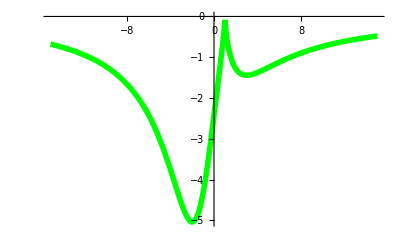

{{-15,-(8 3^(1/3))/17},{-14,-12/59 2^(1/3) 5^(2/3)},{-13,-3/19 3^(1/3) 7^(2/3)},{-12,-4/43 6^(1/3) 13^(2/3)},{-11,-(2 2^(2/3))/3},{-10,-12/89 6^(1/3) 11^(2/3)},{-9,-(5/3)^(2/3)},{-8,-12/19 2^(1/3) 3^(2/3)},{-7,-(12 6^(1/3))/11},{-6,-4/11 6^(1/3) 7^(2/3)},{-5,-3},{-4,-12/17 5^(2/3) 6^(1/3)},{-3,-2 2^(2/3) 3^(1/3)},{-2,-4 2^(1/3)},{-1,-3 3^(1/3)},{0,-(4 2^(1/3))/3^(2/3)},{1,0},{2,-(12 6^(1/3))/17},{3,-3^(1/3)},{4,-(12 2^(1/3))/11},{5,-6/11 2^(2/3) 3^(1/3)},{6,-4/19 5^(2/3) 6^(1/3)},{7,-1},{8,-12/89 6^(1/3) 7^(2/3)},{9,-(4 2^(1/3))/(3 3^(2/3))},{10,-12/43 2^(1/3) 3^(2/3)},{11,-3/19 3^(1/3) 5^(2/3)},{12,-4/59 6^(1/3) 11^(2/3)},{13,-(6 2^(2/3))/17},{14,-12/233 6^(1/3) 13^(2/3)},{15,-1/11 3^(1/3) 7^(2/3)}}

-15. | -0.678706
-14. | -0.749295
-13. | -0.83331
-12. | -0.934554
-11. | -1.05827
-10. | -1.21182
-9. | -1.40572
-8. | -1.65521
-7. | -1.98231
-6. | -2.41796
-5. | -3.
-4. | -3.75056
-3. | -4.57886
-2. | -5.03968
-1. | -4.32675
0. | -2.42283
1. | 0.
2. | -1.28267
3. | -1.44225
4. | -1.37446
5. | -1.24878
6. | -1.11859
7. | -1.
8. | -0.896548
9. | -0.807609
10. | -0.73137
11. | -0.665868
12. | -0.609331
13. | -0.560259
14. | -0.517414
15. | -0.479785

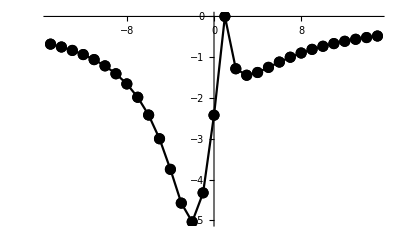

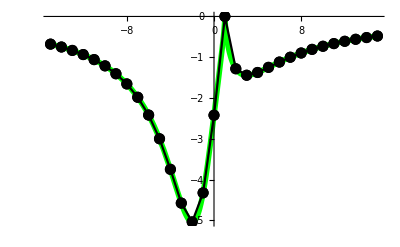

```mathematica
Remove[y,p1,pt,p2]
y[x_]= -12 (6 (x-1)^2)^(1/3)/(x^2+2 x+9);
p1 = Plot[y[x],{x,-15,15},PlotStyle->{Thickness[0.010],Green}]
pt = Table[{x,y[x]},{x,-15,15,1}]
N[pt]//TableForm
p2 = ListPlot[pt,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Black}]
Show[p1,p2]
```

Завдання 2. Побудова графіка полінома

Задача 6.2.3. Використовуючи систему «Mathematica», побудувати графік функції y(x). Інтервал для незалежної змінної підібрати самостійно.

(-1+2 x)^2 (1+2 x)^2

(1-4 x^2)^2

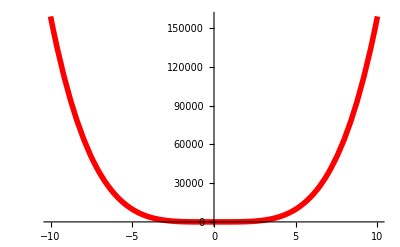

```mathematica
Remove[x,y]
y[x_]=(2 x+1)^2 (2 x-1)^2
Simplify[(2 x+1)^2 (2 x-1)^2]
Plot[y[x],{x,-10,10},PlotStyle->{Thickness[0.01],Red}]
```

Завдання 3. Побудова графіка явно заданої функції.

Задача 6.3.3. Використовуючи систему «Mathematica», побудувати графікфункції y(x). Інтервал для незалежної змінної підібрати самостійно.

6 ⅇ^(-1+x)-3 x-x^3

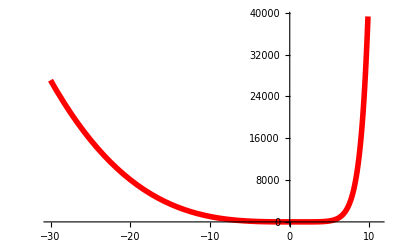

```mathematica
Remove[x,y]
y[x_]=6 ⅇ^(x-1)-3 x-x^3
Plot[y[x],{x,-30,11},PlotStyle->{Thickness[0.01],Red}]
```

Завдання 4. Побудова графіка параметрично заданої функції по точках.

Використовуючи систему «Mathematica», побудувати графік функції, яка задана параметрично. Побудувати таблицю координат вузлів ламаної на інтервалі[0,2 π]. Побудувати її графік, використовуючи цю таблицю значень. На одному малюнку одночасно зобразити графік функції та ламаної

2 √2 Cos[t]

3 √2 Sin[t]

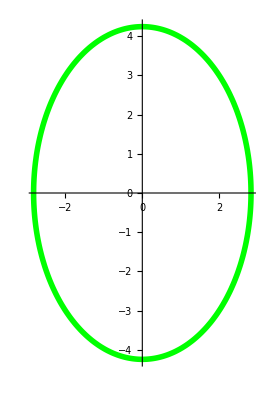

{{2 √2,0},{2,3},{0,3 √2},{-2,3},{-2 √2,0},{-2,-3},{0,-3 √2},{2,-3},{2 √2,0}}

2.82843 | 0.
2. | 3.
0. | 4.24264
-2. | 3.
-2.82843 | 0.
-2. | -3.
0. | -4.24264
2. | -3.
2.82843 | 0.

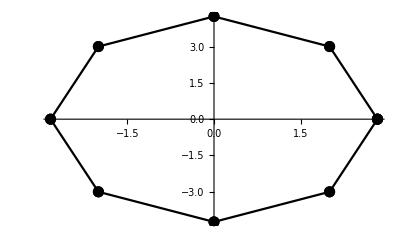

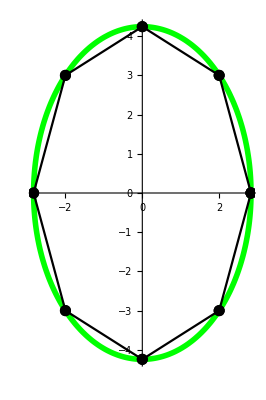

```mathematica
Remove[x,y,t,p1,pt,p2]
x[t_]=2 √2 Cos[t]
y[t_]=3 √2 Sin[t]
p1=ParametricPlot[{x[t],y[t]},{t,0,2 π},AspectRatio->Automatic,
PlotStyle->{Thickness[0.01],Green}]
pt=Table[{x[t],y[t]},{t,0,2 π,π/4}]
N[pt]//TableForm
p2=ListPlot[pt,Joined->True,Mesh->Full,PlotStyle->{PointSize[0.02],Black}]
Show[p1,p2]
```

Завдання 5. Побудова графіка функції, яка задана параметрично.

Задача 6.5.3. Використовуючи систему «Mathematica», побудувати графік функції, яка задана параметрично.

2 t Cos[t]+(-2+t^2) Sin[t]

(2-t^2) Cos[t]+2 t Sin[t]

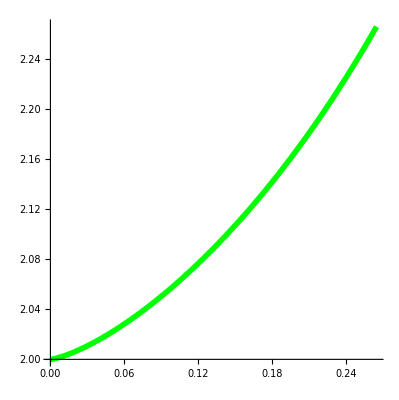

```mathematica
Remove[x,y,t,p1]
x[t_]=(t^2-2) Sin[t]+2 t Cos[t]
y[t_]=(2-t^2) Cos[t]+2 t Sin[t]
p1=ParametricPlot[{x[t],y[t]},{t,0,π/3},AspectRatio->Automatic,
PlotStyle->{Thickness[0.01],Green}]
```

Завдання 6. Побудова графіка функції, яка задана неявно.

Задача 6.5.3. Використовуючи систему «Mathematica», побудувати графік функції, яка задана неявно. Діапазони зміни незалежних змінних підібрати самостійно.

1-2 x-2 y-2 x y

{{x→(1-2 y)/(2+2 y)}}

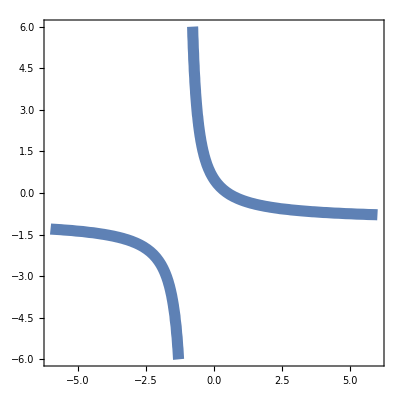

```mathematica
Remove[x,y,F]
F[x_,y_]=-2 x y-2 x-2 y+1
Simplify[Solve[-2 x y-2 x-2 y+1==0,x]]
ContourPlot[F[x,y]==0,{x,-6,6},{y,-6,6},ContourStyle->{Thickness[0.02]}]
```

## Тема 7.Геометричні побудови.

Завдання 1. Побудова площини по трьом точкам.

Задача 7.1.3. Скласти рівняння площини, яка проходить через точки A, B та C. Графічно зобразити точки та площину. Діапазон зміни x,y,z підібрати так, щоб точки були розташовані на площині.

```mathematica
Unprotect[C,D];
Remove[A,B,C,D,p1,P,Eq,p2,z]
A={-3,-1,1};
B={-9,1,-2};
C={3,-5,4};
p1=ListPlot3D[{A,B,C},PlotStyle->{Directive[PointSize[0.03],Red]}];
P={x,y,z};
Eq=Det[{P-A,B-A,C-A}]
Eq==0
p2=ContourPlot3D[Eq==0,{x,-10,10},{y,-6,6},{z,-5,5},Mesh->None,ContourStyle->Opacity[0.5]];
Show[p1,p2,PlotRange->All,AspectRatio->Automatic]
```

-30-6 x+12 z

-30-6 x+12 z==0

-Graphics3D-

Завдання 2. Паралелограм в просторі.

Задача 7.2.3. В просторі дано плоский паралелограм, координати трьох вершин A, B, C якого відомі. Знайти координати четвертої вершини D, яка протилежна вершині A. Обчислити площу паралелограма. В системі Mathematica побудувати контур паралелограма, та його вершини.

```mathematica
Unprotect[C,D];
Remove[A,B,C,AB,AC,D,p1,p2,S]
A={3,3,-1};B={5,5,-2};C={4,1,1};
AB=B-A;
AC=C-A;
D=A+(AB+AC)
p1=Graphics3D[{Thickness[0.01],Line[{A,B,D,C,A}]}];
p2=ListPointPlot3D[{A,B,D,C},PlotStyle->{Directive[PointSize[0.03],Red]}];
Show[p1,p2]
S=Norm[Cross[AB,AC]]
```

{6,3,0}

-Graphics3D-

√65

Завдання 3. Обчислення в просторовому трикутнику.

У трикутника з вершинами в точках A, B, C знайти висоту h=|OverVector[BD]|, яка проведена з вершини B на протилежну сторону. Знайти також довжину медіани, проведеної із вершини B на протилежну сторону. В системі Mathematica побудувати контур трикутник, та його медіану.

```mathematica
Unprotect[C];
Remove[A,B,C,AB,AC,p1,p2,S,LAC,BA,BC,BM,M,h]
A={0,3,-6};B={-4,3,6};C={4,3,3};
p1=Graphics3D[{Thickness[0.02],Line[{A,B,C,A}]}];
AB=B-A;
AC=C-A;
S=1/2 Norm[Cross[AB,AC]]
LAC=Norm[AC]
Solve[1/2 h*LAC==S,h ]
BA=A-B;
BC=C-B;
BM=(BA+BC)/2
Norm[BM]
M=B+BM
p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{B,M}]}];
Show[p1,p2,Axes->True,AxesLabel->{"X","Y","Z"}]
```

42

√97

{{h→84/(√97)}}

{6,0,-15/2}

(3 √41)/2

{2,3,-3/2}

-Graphics3D-

Завдання 4. Пряма і площина у просторі.

Задача 7.4.3. Знайти точку перетинання прямої і площини. Використовуючи систему «Mathematica», намалювати пряму, площину і точку їх перетинання.

```mathematica
Remove[x,y,z,t,rez,t0,pl,pp,pt]
x[t_]=1 t+5;
y[t_]=-1 t+3;
z[t_]=0 t+2;
rez=Solve[3 x-8 y-5 z-12==0/.{x->x[t],y->y[t],z->z[t]},t]
t0=t/.rez[[1]]
{x0,y0,z0}={x[t0],y[t0],z[t0]}
pl=ParametricPlot3D[{x[t],y[t],z[t]},{t,-10,20},PlotStyle->Thickness[0.02]];
pp=ContourPlot3D[3 x-8 y-5 z-12==0,{x,10,-10},{y,10,-10},{z,10,-10},Mesh->False];
pt=ListPointPlot3D[{{x0,y0,z0}},PlotStyle->{Directive[PointSize[0.05],Red]}];

Show[pl,pp,pt,PlotRange->All]
```

{{t→31/11}}

31/11

{86/11,2/11,2}

-Graphics3D-

## Тема 8. Анімація. Робота з документами Mathematica

Завдання 1. Анімація кривої.

Задача 8.1.3. Побудувати анімацію руху кривої на заданому відрізку часу.

```mathematica
Remove[x,t]
Animate[Plot[0.5 (Sin[x-t]+Sin[x+t]),{x,0,π},PlotRange->1,PlotLabel->t],{t,0,2π},AnimationRunning->False]
```

Завдання 2. Анімація руху точки вздовж кривої.

Задача 8.2.3. Побудувати анімацію руху точки вздовж заданого відрізка параметричної кривої.

```mathematica
Remove[x,y,t,p1,p2]
x[t_]=(t^2-2) Sin[t]+2 t Cos[t];
y[t_]=(2-t^2) Cos[t]+2 t Sin[t];
p1=ParametricPlot[{x[tau],y[tau]},{tau,0,π}];
Animate [p2=Graphics[{Green,Disk[{x[t],y[t]},0.15]}];
Show[p1,p2],{t,0.1,π}]
```

## Тема 9. Послідовність з раціональним загальним членом

Завдання 1. Послідовність з раціональним загальним членом.

Задача 9.1.3. Використовуючи систему «Mathematica», обчислити границю послідовності та надрукувати вісім початкових членів.

```mathematica
Remove[x,n]
x[n_]=((n+1)^2+(n-1)^2-(n+2)^3)/(4+n)^3;
Table[x[n],{n,1,8}]
N[Table[x[n],{n,1,8}]]
Limit[x[n],n->∞]
```

{-23/125,-1/4,-15/49,-91/256,-97/243,-219/500,-629/1331,-145/288}

{-0.184,-0.25,-0.306122,-0.355469,-0.399177,-0.438,-0.472577,-0.503472}

-1

Завдання 2. Послідовність з ірраціональним загальним членом

Задача 9.2.3 Використовуючи систему «Mathematica», обчислити границю послідовності, надрукувати 8 початкових членів в десятковому вигляді, побудувати графік перших 50 членів.

{-1.2,17.2,2.63,1.73,1.38,1.19,1.06,0.967}

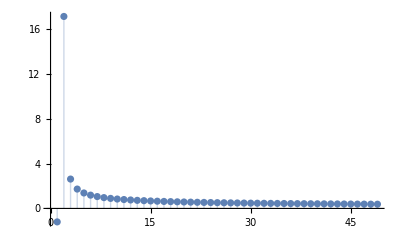

0

```mathematica
Remove[x,n]
x[n_]=(√(n+2)-√(n^2+2))/((4 n^4+1)^(1/4)-(n^4-1)^(1/3));
N[Table[x[n],{n,2,9}],3]
ListPlot[Table[x[n],{n,2,50}],Filling->Axis,PlotRange->All]
Limit[x[n],n->∞]
```

Завдання 3. Границі різноманітних функцій.

Задача 9.3.3Використовуючи систему «Mathematica», обчислити границю функції. Перевірити, що значення функції наближаються до границі, коли аргумент x прямує до граничного значення x0. Для цього побудуйте таблицю значень функції в околі граничного значення x0.

```mathematica
Remove[f,x,n,x0,y0]
f[x_]=(1-x^2)/(Sin [π x])
x0=0;
y0=Limit[f[x],x->x0]
f[x0+{0.1,0.01,0.001,0.00001,0.000001}]
```

(1-x^2) Csc[π x]

Indeterminate

{3.20371,31.833,318.31,31831.,318310.}

Завдання 4. Границі функцій в околі особливої точки.

Задача 9.4.3. Використовуючи систему «Mathematica», обчислити границю функції. Перевірити, що гранична точка є особливою точкою функції. Показати, що значення функції наближаються до граничного, коли аргумент x прямує до граничного значення. Для цього побудувати графік функції і особливу точку. Діапазон для незалежної змінної підібрати самостійно.

(1-Cos[x]^3)/(4 x^2)

1/36 (1-Cos[3]^3)

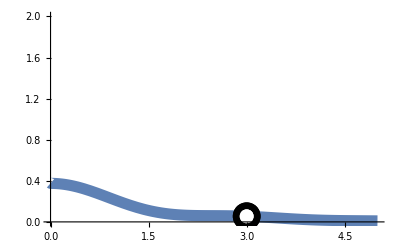

```mathematica
Remove[x,n,f,x0,y0,pw,pf,pline]
f[x_]=(1-Cos[x]^3)/(4 x^2)
x0=3;
y0=Limit[f[x],x->x0]
pf=ListPlot[{{x0,y0}},PlotStyle->{Black,PointSize[0.05]}];
pw=ListPlot[{{x0,y0}},PlotStyle->{White,PointSize[0.025]}];
pline = Plot[f[x],{x,0,5},PlotStyle->Thickness[0.02]];
Show[pline,pf,pw,PlotRange->{{0,5},{0,2}},AxesOrigin->{0,0}]
```

Завдання 5. Обчислення похідних

Задача 9.5.3. Використовуючи систему «Mathematica», обчислити похідну y'(x) функції y(x). Побудувати графік функції y(x) та її похідноїy'(x). Обчислити значення похідної в точках x = 3, 5.0, 7.

(√((1-√x)/(1+√x)))/((-1+x) √x)

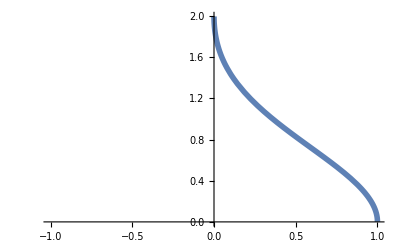

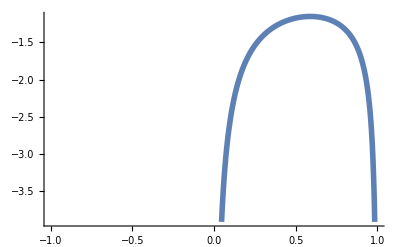

{1/2 ⅈ √((-1+√3)/(3 (1+√3))),0.+0.0690983 ⅈ,1/6 ⅈ √((-1+√7)/(7 (1+√7)))}

```mathematica
Remove[y,x,y1]
y[x_]=2 √((1-√x)/(1+√x));
y1[x_]=Simplify[D[y[x],x]]
Plot[y[x],{x,-1,1},PlotStyle->Thickness[0.01]]
Plot[y1[x],{x,-1,1},PlotStyle->Thickness[0.01]]
y1[{3,5.0,7}]
```

Завдання 6. Похідні виразів, які містять тригонометричні функції.

Задача 9.6.3. Використовуючи систему «Mathematica», знайти похідну функції y(x)та побудувати її графік.

1/3 Cos[Tan[1/2]]+1/10 Sec[20 x] Sin[10 x]^2

Sec[20 x] Tan[20 x]

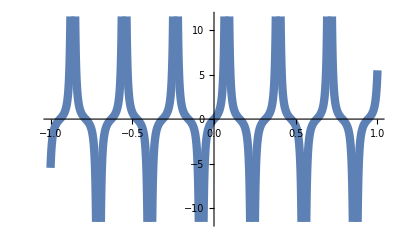

```mathematica
Remove[y,y1]
y[x_]=1/3 Cos[Tan[1/2]]+1/10 Sin[10 x]^2/Cos[20 x]
y1[x_]=Simplify[D[y[x],x]]
Plot[y1[x],{x,-1,1},PlotStyle->Thickness[0.015]]
```

Завдання 7. Похідні вищих порядків.

Задача 9.7.3. Використовуючи систему «Mathematica», знайти похідну зазначеного порядку та побудувати її графік.

-1/16 ⅇ^(1/2 (-1+x)) (55+17 x+x^2)

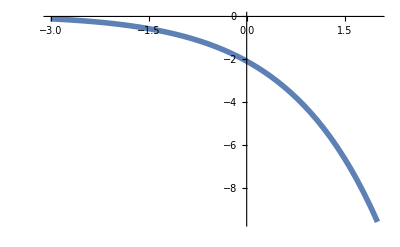

```mathematica
Remove[y,x,y1,y4]
y[x_]= (1-x-x^2) ⅇ^((x-1)/2);
y4[x_]=Simplify[D[y[x],{x,4}]]
Plot[y4[x],{x,-3,2},PlotStyle->Thickness[0.01]]
```

Завдання 8. Використання похідних у рівняннях

Використовуючи систему «Mathematica», показати, що функція y(x) задовольняє рівнянню. В кожному варіанті задана функція та рівняння, якому вона можливо задовольняє

```mathematica
Remove[y,x,y1,y4]
y[x_]= -√(x^3-x);
y1[x_]=Simplify[D[y[x],x]]
Simplify[x*y[x]*y1[x]-y[x]^2==1/2 (x+x^3)]
```

(1-3 x^2)/(2 √(x (-1+x^2)))

True

## Тема 10. Використання диференціального числення

Завдання 1. Графік дотичної

Задача 10.1.3. Використовуючи систему «Mathematica», скласти рівняння дотичної до кривої в точці з абсцисою х0 x. Побудувати графіки функції і її дотичної в цій точці. Діапазони зміни x на графіках кривої та дотичної підбирати самостійно.

4/(√x)+2 x

10 (-4+x)

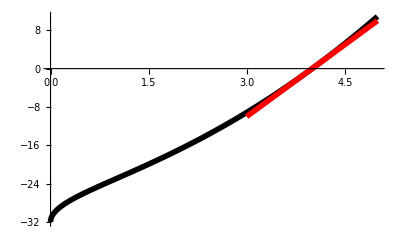

```mathematica
Remove[y,y1,x0,Y,p1,p2]
y[x_]= x^2+8 √x-32;
y1[x_]=D[y[x],x]
x0=4;
Y[x_]=y[x0]+y1[x0](x-x0)
p1=Plot[y[x],{x,0,5},PlotStyle->{Black,Thickness[0.01]}];
p2=Plot[Y[x],{x,x0-1,x0+1},PlotStyle->{Red,Thickness[0.01]}];
Show[p1,p2,PlotRange->All]
```

Завдання 2. Дотична та нормаль до параметричної кривої.

Задача 10.2.3. Використовуючи систему «Mathematica», скласти рівняння дотичної та нормалі до параметрично заданої кривої в зазначеній точці t0. Побудувати графіки кривої, дотичної і нормалі в цій точці. При побудові графіків підбирати діапазони зміни параметра t так, щоб крива, точка і прямі відображали свої характерні ділянки в околі точки дотику.

3/2-t/4

1/2-(3 t)/4

3/2-(3 t)/4

1/2+t/4

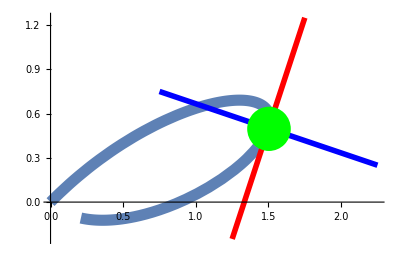

```mathematica
Remove[x,y,t,t0,xt,yt,xn,yn,p1,p2,p3,p4]
x[t_]=(2 t+t^2)/(1+t^3);
y[t_]= (2 t-t^2)/(1+t^3);
t0=1;
xt[t_]=x[t0]+t*x'[t0]
yt[t_]=y[t0]+t *y'[t0]
xn[t_]=x[t0]+t*y'[t0]
yn[t_]=y[t0]-t*x'[t0]
p1=ParametricPlot[{x[t],y[t]},{t,0,2 π},PlotStyle->Thickness[0.02],AspectRatio->Automatic];
p2=Graphics[{Green,Disk[{x[t0],y[t0]},0.15]}];
p3=ParametricPlot[{xt[t],yt[t]},{t,-1,1},PlotStyle->{Red,Thickness[0.01]}];
p4=ParametricPlot[{xn[t],yn[t]},{t,-1,1},PlotStyle->{Blue,Thickness[0.01]}];
Show[p1,p3,p4,p2,PlotRange->All]
```

Завдання 3. Асимптоти.

Задача 10.3.3. Використовуючи систему «Mathematica», знайти асимптоти функції y(x) . Побудувати графік функції та всі її похилі і горизонтальні асимптоти. Якщо у функціх є вертикальні асимптоти в точках x_i, то ці точки виключити з графіка.

1/2

0

{{x→-(√3)/2},{x→(√3)/2}}

Indeterminate

Indeterminate

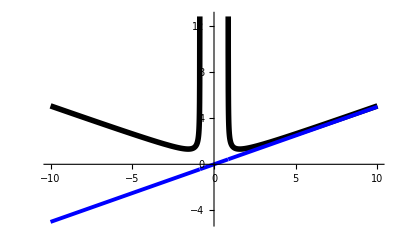

```mathematica
Remove[f,a,b]
f[x_]=(x^2+1)/(√(4 x^2-3));
a = Limit[f[x]/x,x->∞]
b=Limit[f[x]-a x,x->∞]
Solve[√(4 x^2-3)==0,x,Reals]
Limit[f[x],x->(√3)/2]
Limit[f[x],x->-(√3)/2]
Plot[{f[x],a x+b},{x,-10,10},PlotStyle->{{Black,Thickness[0.01]},{Blue,Thickness[0.007]}},Exclusions->{-(√3)/2,(√3)/2}]
```

Завдання 4. Дотична і нормаль до кривої, яка задана неявно

Задача 10.4.3. Використовуючи систему «Mathematica», скласти рівняння дотичної та нормалі до кривої, яка задана неявно. Побудувати графіки кривої, її дотичної та нормалі в точці, яку вибрати самостійно.

-15+4 x+x^2+y+4 x y+4 y^2

{{y→1/8 (-9-√129)},{y→1/8 (-9+√129)}}

1/8 (-9+√129)

(8+1/2 (-9+√129)) (-2+x)+√129 (1/8 (9-√129)+y)

√129 (-2+x)+(8+1/2 (-9+√129)) (1/8 (9-√129)+y)

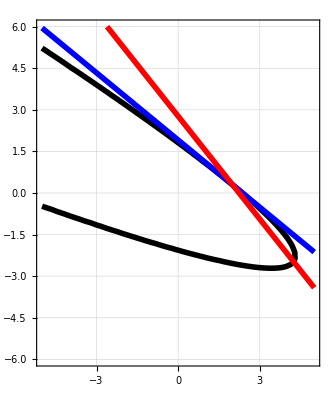

```mathematica
Remove[pc1,F,x0,rez,y,x,y0,eqT,eqN,pc2]
F[x_,y_]=x^2+4 x y+4 y^2+4 x+y-15
pc1=ContourPlot[F[x,y]==0,{x,-5,5},{y,-6,6},ContourStyle->{Black,Thickness[0.01]}];
x0=2;rez=Solve[F[x0,y]==0,y]
y0=rez[[2]][[1,2]]
eqT=Derivative[1,0][F][x0,y0](x-x0)+Derivative[0,1][F][x0,y0](y-y0)
eqN=Derivative[1,0][F][x0,y0](y-y0)+Derivative[0,1][F][x0,y0](x-x0)
pc2=ContourPlot[{eqT==0,eqN==0},{x,-5,5},{y,-6,6},ContourStyle->{{Blue,Thickness[0.01]},
{Red,Thickness[0.01]}}];
Show[pc1,pc2,AspectRatio->Automatic,GridLines->Automatic]
```

Завдання 5. Найбільше та найменше значення функції.

Задача 10.5.3. Використовуючи систему «Mathematica», знайти найбільше та найменше значення функції y(x) на заданому відрізку. Побудувати графік функції на відрізку, та позначити на графіку екстремальні точки.2 x^2+108/x-59;

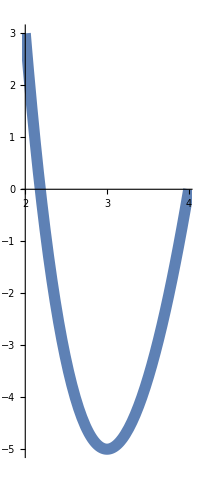

{-5,{x→3}}

{3,{x→2}}

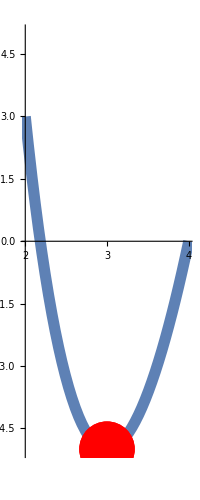

```mathematica
Remove[x,y,p1,min,ymin,ymax,xmin,xmax,p2]
y[x_]=2 x^2+108/x-59;
p1=Plot[y[x],{x,2,4},PlotStyle->Thickness[0.02],AspectRatio->Automatic]
min =Minimize[{y[x],2≤x≤4},x]
ymin=min[[1]];
xmin=x/.min[[2]];
max=Maximize[{y[x],2≤x≤4},x]
ymax=min[[1]];
xmax=x/.min[[2]];
p2=ListPlot[{{xmin,ymin},{xmax,ymax}},PlotStyle->{Red,PointSize[0.1]}];
Show[p1,p2,PlotRange->{{2,4},{-5,5}}]
```

Завдання 6. Частинні похідні. Нормаль до поверхні.

Задача 10.6.3. Використовуючи систему «Mathematica», обчислити частинні похідні першого і другого порядків функції. Побудувати графік функції і вектор нормалі до її поверхні в заданій точці. Щоб нормаль до поверхні виглядала як  нормаль, підібрати пропорції довжин координатних осей графіка, використовуючи опцію BoxRatios.

```mathematica
Remove[x,y,z,x0,y0,P]
z[x_,y_]=x y -y/(x^2+1);
zx[x_,y_]=D[z[x,y],x]
zy[x_,y_]=D[z[x,y],y]
Simplify[D[z[x,y],{x,2}]]
Simplify[D[z[x,y],{x,y}]]
Simplify[D[z[x,y],{y,2}]]
x0=0.5 ;y0=0.5;
P={x0,y0,z[x0,y0]}
n={zx[x0,y0],zy[x0,y0],-1}
p1=Plot3D[z[x,y],{x,-1,1},{y,-1,1},PlotRange->All,Mesh->None];
p2=Graphics3D[{Thickness[0.02],Arrowheads[0.1],Arrow[{P,P+n}]}];
Show[p1,p2,BoxRatios->{2,4,3},AxesLabel->{"X","Y","Z"}]
```

y+(2 x y)/((1+x^2)^2)

x-1/(1+x^2)

((2-6 x^2) y)/((1+x^2)^3)

(Piecewise[{{-(Piecewise[{{y (Piecewise[{{-1/2 ⅈ ((-ⅈ-x)^(-1-y)-(ⅈ-x)^(-1-y)) y!, y≥1}, {1/(1+x^2), True}}]), y≥1}, {y/(1+x^2), True}}]), y≥1}, {-y/(1+x^2), True}}])+(Piecewise[{{y, y==1}, {x y, y<1}, {0, True}}])

0

{0.5,0.5,-0.15}

{0.82,-0.3,-1}

-Graphics3D-

## Тема 11. Невизначений та визначений інтеграл. Кратні інтеграли.

Завдання 1. Обчислення невизначеного інтеграла.

Задача 11.1.3. Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графіки підінтегрального виразу та первісної.

-1/4 √(-1+4 x)+x ArcTan[√(-1+4 x)]

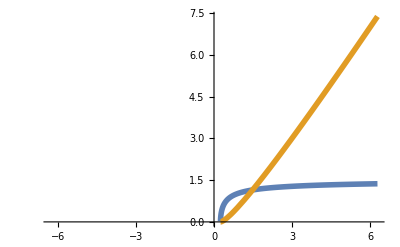

```mathematica
Remove[f,F]
f[x_]=ArcTan[√(4 x-1)];
F[x_]=Integrate[f[x],x]
Plot[{f[x],F[x]},{x,-2 π,2 π},PlotStyle->Thickness[0.01]]
```

Завдання 2. Невизначений інтеграл різноманітних функцій

Задача 11.2.3. Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графік підінтегрального виразу та його первісної.

-Csc[x]/x

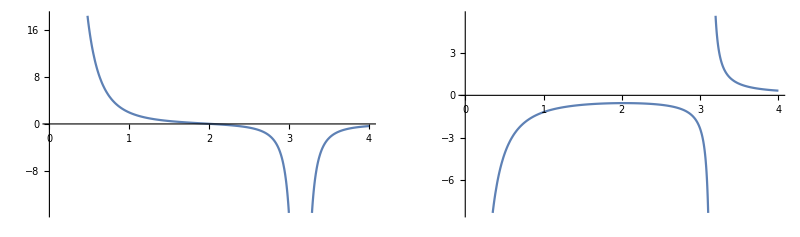

```mathematica
Remove[f,g,p1,p2,x]
f[x_]=(x Cos[x]+Sin[x])/(x Sin[x])^2;
g[x_]=∫f[x]ⅆx
p1= Plot[f[x],{x,0,4}];
p2 =Plot[g[x],{x,0,4}];
GraphicsRow[{p1,p2}]
```

Завдання 3. Невизначений інтеграл раціональних функцій.

Задача 11.3.3. Використовуючи систему «Mathematica», обчислити невизначений інтеграл. Побудувати графіки підінтегрального виразу, виключивши з нього особливі точки.

1/x^3+1/(2+x)

-1/(2 x^2)+Log[2+x]

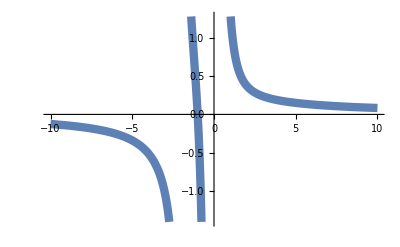

```mathematica
Remove[f,g,p1,p2,x,q]
f[x_]=(x^3+x+2)/((x+2) x^3);
q[x_]=Apart[f[x]]
F[x_]=∫q[x]ⅆx
Plot[f[x],{x,-10,10},PlotStyle->Thickness[0.015]]
```

Завдання 4. Обчислення визначеного інтеграла

Задача 11.4.3. Використовуючи систему «Mathematica», обчислити визначений інтеграл. Графічно зобразити зону, площу якої він представляє.

3/4+2 Log[2]^2-Log[4]

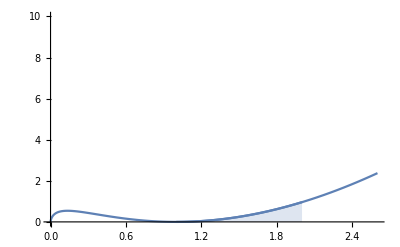

```mathematica
Remove[f,g,p1,p2,x,q,s]
f[x_]=x Log[x]^2;
s=Integrate[f[x],{x,1,2}]
p1=Plot[f[x],{x,1,2},Filling->Axis];
p2=Plot[f[x],{x,0,2.6}];
Show[p1,p2,PlotRange->{{0,2.6},{0,10}},AxesOrigin->{0,0}]
```

Завдання 5. Визначений інтеграл різноманітних функцій

Задача 11.5.3. Використовуючи систему «Mathematica», обчислити визначений інтеграл. Графічно зобразити зону, площу якої він представляє

π^2/18+Log[2]

1.24146

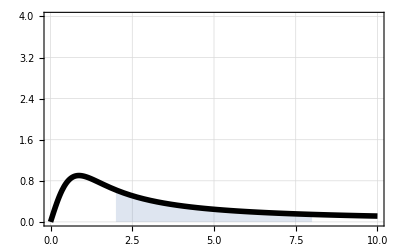

```mathematica
Remove[f,g,p1,p2,x,q,s]
f[x_]=(ArcTan[x]+x)/(1+x^2);
s=∫_0^(√3) f[x]ⅆx
s=N[s]
p1=Plot[f[x],{x,2,8},Filling->Axis,AxesOrigin->{0,0}];
p2=Plot[f[x],{x,0,10},PlotStyle->{Thickness[0.01],Black}];
Show[{p1,p2},PlotRange->{{0,10},{0,4}},Frame->True,GridLines->Automatic]
```

Завдання 6. Визначений інтеграл від тригонометричних виразів.

Задача 11.6.3. Використовуючи систему «Mathematica», обчислити визначений інтеграл. Графічно зобразити зону, площу якої він представляє.

(5 π)/64

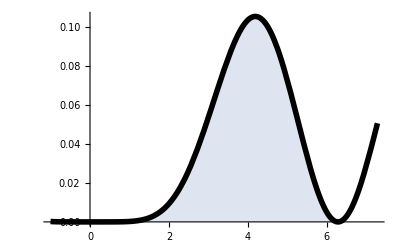

```mathematica
Remove[f,g,p1,p2,x,q,s]
f[x_]=Sin[x/4]^6 Cos[x/4]^2;
s=∫_0^(2 π) f[x]ⅆx
p1=Plot[f[x],{x,0,2 π},Filling->Axis,AxesOrigin->{0,0}];
p2 =Plot[f[x],{x,-1,2 π+1},PlotStyle->{Thickness[0.01],Black}];
Show[{p1,p2},PlotRange->All]
```

Завдання 7. Подвійний інтеграл як повторний.

Задача 11.7.3. Використовуючи систему «Mathematica», обчислити подвійний
інтеграл по області D як повторний. Графічно зобразити область D.

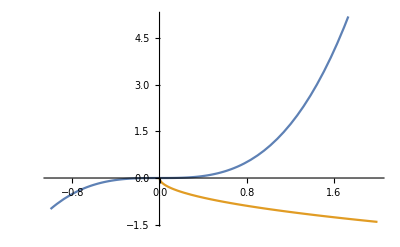

{{x→0}}

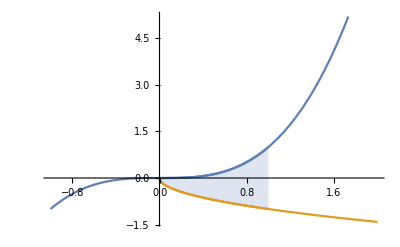

x y-4 x^3 y^3

0

```mathematica
Remove[f,g,p1,p2,x,q,s,y1,y2]
y1[x_]= x^3;
y2[x_]=-√x;
p1=Plot[{y1[x],y2[x]},{x,-1,2 }]
Solve[y1[x]==y2[x],x,Reals]
p2 =Plot[{y1[x],y2[x]},{x,0,1 },Filling->{1->{2}}];
Show[p1,p2]
f[x_,y_]=x y-4 x^3 y^3
Integrate[f[x,y],{x,0,1},{y,-√x,x^3}]
```

Завдання 8. Обчислення подвійного інтеграла.

Задача 11.8.3. Використовуючи систему «Mathematica», обчислити подвійний
інтеграл по області D як повторний. Графічно зобразити область D.

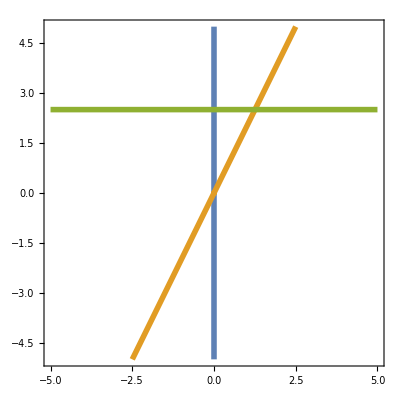

```mathematica
Remove[f,g,p1,p2,x,q,s,y1,y2]
p1=ContourPlot[{x-0==0,y-2 x==0,y-√(2 π)==0},{x,-5,5},{y,-5,5},ContourStyle->Thickness[0.01]]
p2= Graphics[{LightGray,Polygon[{{
```